```mathematica
LogIntegralEurope[x_]:=LogIntegral[x]-LogIntegral[2]
```

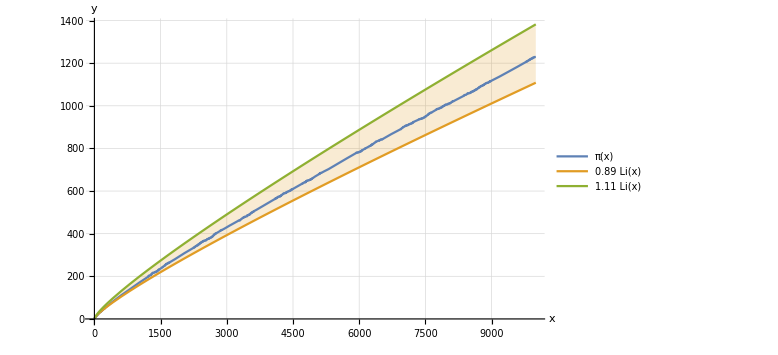

/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/chebyshev-bounds.pdf

```mathematica
Plot[{PrimePi[x], 0.89LogIntegralEurope[x],1.11LogIntegralEurope[x]},{x,0,10001},AxesLabel->{x,y}, ImageSize->Large, PlotTheme->"Default", PlotLegends->{Pi[x],  0.89Li[x],1.11Li[x]},GridLines->Automatic, Filling->{2-> {3}}]
Export["/Users/Flo/Dropbox/Schule/3. W-Seminar/jupyter/zeta/chebyshev-bounds.pdf",%,"PDF"]
```